## Fundamental Solution

```mathematica
DSolve[f''[x]+3/x f'[x]-A/x f[x]==-4π q/x DiracDelta[x],f[x],x]//FullSimplify
```

{{f[x]→(2 BesselK[2,2 √A √x] C[2])/(A x)+(C[1]+2 π q HeavisideTheta[-x]) Hypergeometric0F1[3,A x]}}

```mathematica
u1[x_,a_]:=BesselI[2,2 √a √x]/(a x);
```

```mathematica
D[u1[x,a],{x,2}]+3/x D[u1[x,a],x]-a/x u1[x,a]//FullSimplify
```

0

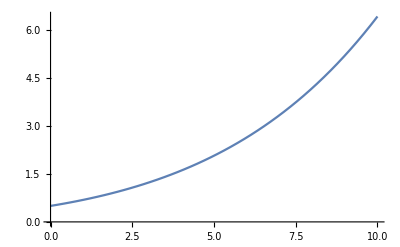

```mathematica
Plot[u1[x,1],{x,0,10}]
```

```mathematica
u2[x_,a_]:=BesselK[2,2 √a √x]/(a x);
```

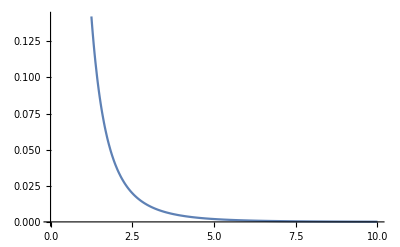

```mathematica
Plot[u2[x,1],{x,0,10}]
```

```mathematica
Assuming[x∈Reals&&x>0&&f∈Reals&&f>0&&α∈Reals&&α>0&&m∈Reals&&m>0,Series[(2 m^4 f^3)/α^2 u2[x,m^2 f/α],{m,0,3}]]//FullSimplify
```

f/x^2-(f^2 m^2)/(x α)+O[m]^4